```mathematica
basis={{1,0},{0.5,-Sqrt[3]/2}};
```

{{1,0},{0.5,-(√3)/2}}

```mathematica
latticePoints=Flatten[Table[(i*basis[[1]]+j*basis[[2]]),{i,-5,5},{j,-5,5}],1];
```

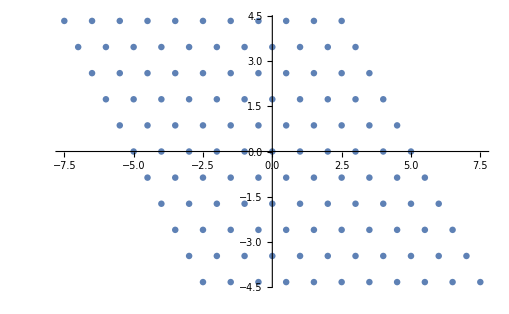

```mathematica
ListPlot[latticePoints]
```

```mathematica
triangularCell[a_Integer,b_Integer]:=a*basis[[1]]+b*basis[[2]];
triangularCell[1,1]
```

{1.5,-(√3)/2}

```mathematica
triangularCellCenter[a_Integer,b_Integer]:=(a+0.5)basis[[1]]+(b+0.5)
```